```mathematica
Quit[]
```

```mathematica
$LoadFeynArts=True;
<<FeynCalc`
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

FeynArts 3.11 (2 Sep 2019) patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

```mathematica
$FAVerbose=0;
```

# Loop Contribution

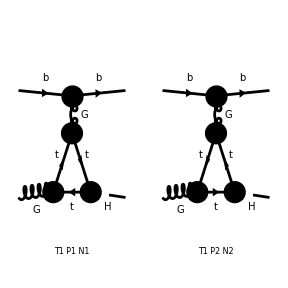

FeynArtsGraphics({b,G}→{b,H})(([T1 P1 N1] | [T1 P2 N2] | Null
Null | Null | Null
Null | Null | Null))

```mathematica
diagloop=InsertFields[CreateTopologies[1,2->2,ExcludeTopologies->{Tadpoles,SelfEnergies,AllBoxes}],{F[12],V[4]}->{F[12],S[1]},InsertionLevel->{Particles},Model->{"htt"},GenericModel->{"htt"},LastSelections->{V[4],F[9]}];
Paint[diagloop]
```

```mathematica
amploop=FCFAConvert[CreateFeynAmp[diagloop,Truncated->True],IncomingMomenta->{p[1],p[2]},OutgoingMomenta->{p[3],p[4]},LoopMomenta->{l},DropSumOver->True,UndoChiralSplittings->True,ChangeDimension->4,SMP->True]/.M$FACouplings/.{FAGS->gs,ybcky->yt};
```

```mathematica
amploop=Plus@@amploop/.{DiracTrace->TR}//SUNSimplify//ChangeDimension[#,D]&//TID[#,l,ToPaVe->True]&//ChangeDimension[#,4]&//ReplaceAll[#,{D->4}]&//Simplify;
```

```mathematica
amploop
```

-1/(8 √2 π^2 (OverBar[p(4)]-OverBar[p(2)])^2 (t-(SMP(m_h))^2)^3)gs^3 yt m_t T_Col3Col1^Glu2 ((t-(SMP(m_h))^2) (C_0(0,t,(SMP(m_h))^2,m_t^2,m_t^2,m_t^2) (-2 sin(al) (γ̄)^Lor3 (t-(SMP(m_h))^2)^2 ϵ^(Lor1Lor3 OverBar[p(2)]OverBar[p(4)])+2 cos(al) OverBar[p(2)]^Lor1 (t-(SMP(m_h))^2) γ̄·OverBar[p(4)] (4 m_t^2+(SMP(m_h))^2+t)+2 cos(al) γ̄·OverBar[p(2)] (4 (2 m_t^2+t) (SMP(m_h))^2 OverBar[p(2)]^Lor1+OverBar[p(4)]^Lor1 (-2 (2 m_t^2+t) (SMP(m_h))^2+t (4 m_t^2+t)+(SMP(m_h))^4))+cos(al) (γ̄)^Lor1 (t-(SMP(m_h))^2)^2 (4 m_t^2-(SMP(m_h))^2+t))-4 cos(al) OverBar[p(2)]^Lor1 B_0(0,m_t^2,m_t^2) ((t-(SMP(m_h))^2) γ̄·OverBar[p(4)]+((SMP(m_h))^2+t) γ̄·OverBar[p(2)]))-2 cos(al) B_0((SMP(m_h))^2,m_t^2,m_t^2) (2 OverBar[p(2)]^Lor1 (t (SMP(m_h))^2-2 (SMP(m_h))^4+t^2) γ̄·OverBar[p(4)]+2 γ̄·OverBar[p(2)] (2 (SMP(m_h))^2 OverBar[p(2)]^Lor1 ((SMP(m_h))^2+2 t)+t OverBar[p(4)]^Lor1 (t-(SMP(m_h))^2))+t (γ̄)^Lor1 (t-(SMP(m_h))^2)^2)+2 cos(al) B_0(t,m_t^2,m_t^2) (2 OverBar[p(2)]^Lor1 (-t (SMP(m_h))^2-(SMP(m_h))^4+2 t^2) γ̄·OverBar[p(4)]+2 γ̄·OverBar[p(2)] (OverBar[p(2)]^Lor1 (4 t (SMP(m_h))^2+(SMP(m_h))^4+t^2)+t OverBar[p(4)]^Lor1 (t-(SMP(m_h))^2))+t (γ̄)^Lor1 (t-(SMP(m_h))^2)^2))

```mathematica
FCClearScalarProducts[]
SetMandelstam[s,t,u,p[1],p[2],-p[3],-p[4],SMP["m_b"],0,SMP["m_b"],SMP["m_h"]];
amploop=amploop//Simplify;
```

```mathematica
beta=Sqrt[4 SMP["m_t"]^2/SMP["m_h"]^2-1];
beta1=Sqrt[1-4 SMP["m_t"]^2/t];
scalarIntegral={_C0->(1/2/(q-SMP["m_h"]^2) (Log[(beta1+1)/(beta1-1)]^2+ ArcTan[2 beta/(1-beta^2)]^2)),
B0[SMP["m_h"]^2,SMP["m_t"]^2,SMP["m_t"]^2]->(1/ep+Log[m^2/MH^2]+2-beta ArcTan[2 beta/(beta^2-1)]-Log[(1+beta^2)/4]),
B0[t,SMP["m_t"]^2,SMP["m_t"]^2]->(1/ep+Log[m^2/(-t)]+2+beta1 Log[beta1-1]-beta1 Log[beta1+1]-Log[(beta1^2-1)/4]),
B0[0,SMP["m_t"]^2,SMP["m_t"]^2]->(1/ep+Log[m^2/MT^2])};
```

```mathematica
Series[amploop/.scalarIntegral,{ep,0,0}]//Simplify
```

1/(8 √2 π^2 (OverBar[p(4)]-OverBar[p(2)])^2 (t-(SMP(m_h))^2)^3)gs^3 yt m_t T_Col3Col1^Glu2 (-(t-(SMP(m_h))^2) (1/(2 (q-(SMP(m_h))^2))((tan^-1((2 √((4 m_t^2)/(SMP(m_h))^2-1))/(2-(4 m_t^2)/(SMP(m_h))^2)))^2+log^2((√(1-(4 m_t^2)/t)+1)/(√(1-(4 m_t^2)/t)-1))) (-2 sin(al) (γ̄)^Lor3 (t-(SMP(m_h))^2)^2 ϵ^(Lor1Lor3 OverBar[p(2)]OverBar[p(4)])+2 cos(al) OverBar[p(2)]^Lor1 (t-(SMP(m_h))^2) γ̄·OverBar[p(4)] (4 m_t^2+(SMP(m_h))^2+t)+2 cos(al) γ̄·OverBar[p(2)] (4 (2 m_t^2+t) (SMP(m_h))^2 OverBar[p(2)]^Lor1+OverBar[p(4)]^Lor1 (-2 (2 m_t^2+t) (SMP(m_h))^2+t (4 m_t^2+t)+(SMP(m_h))^4))+cos(al) (γ̄)^Lor1 (t-(SMP(m_h))^2)^2 (4 m_t^2-(SMP(m_h))^2+t))-4 cos(al) OverBar[p(2)]^Lor1 log(m^2/MT^2) ((t-(SMP(m_h))^2) γ̄·OverBar[p(4)]+((SMP(m_h))^2+t) γ̄·OverBar[p(2)]))+2 cos(al) (log(m^2/MH^2)-log(m_t^2/(SMP(m_h))^2)+√((4 m_t^2)/(SMP(m_h))^2-1) tan^-1(((SMP(m_h))^2 √((4 m_t^2)/(SMP(m_h))^2-1))/((SMP(m_h))^2-2 m_t^2))+2) (2 OverBar[p(2)]^Lor1 (t (SMP(m_h))^2-2 (SMP(m_h))^4+t^2) γ̄·OverBar[p(4)]+2 γ̄·OverBar[p(2)] (2 (SMP(m_h))^2 OverBar[p(2)]^Lor1 ((SMP(m_h))^2+2 t)+t OverBar[p(4)]^Lor1 (t-(SMP(m_h))^2))+t (γ̄)^Lor1 (t-(SMP(m_h))^2)^2)-2 cos(al) (log(-m^2/t)-log(-m_t^2/t)+√(1-(4 m_t^2)/t) log(√(1-(4 m_t^2)/t)-1)-√(1-(4 m_t^2)/t) log(√(1-(4 m_t^2)/t)+1)+2) (2 OverBar[p(2)]^Lor1 (-t (SMP(m_h))^2-(SMP(m_h))^4+2 t^2) γ̄·OverBar[p(4)]+2 γ̄·OverBar[p(2)] (OverBar[p(2)]^Lor1 (4 t (SMP(m_h))^2+(SMP(m_h))^4+t^2)+t OverBar[p(4)]^Lor1 (t-(SMP(m_h))^2))+t (γ̄)^Lor1 (t-(SMP(m_h))^2)^2))+O(ep^1)

```mathematica
Cases[amploop,_B0,Infinity]//DeleteDuplicates//StandardForm
```

{B0[SMP[m_h]^2,SMP[m_t]^2,SMP[m_t]^2],B0[t,SMP[m_t]^2,SMP[m_t]^2],B0[0,SMP[m_t]^2,SMP[m_t]^2]}

```mathematica
spinsum[p_,h_]:=1/4 (1+h GA[5]).(GS[p]+MB).(1-h GA[5]);
```

```mathematica
Clear[tmp];
tmp=Solve[e+Sqrt[e^2+MB^2]==Sqrt[e1^2+MB^2]+Sqrt[e1^2+MH^2],e1]//FullSimplify[#,MB>0 && MH>4 MB && e>0]&;
```

```mathematica
tmp
```

{{e1→-(√(2 e MH^2 √(e^2+MB^2) (2 MB^2-MH^2)+2 e^2 (2 MB^4-2 MB^2 MH^2+MH^4)-4 MB^4 MH^2+MB^2 MH^4))/(2 MB^2)},{e1→(√(2 e MH^2 √(e^2+MB^2) (2 MB^2-MH^2)+2 e^2 (2 MB^4-2 MB^2 MH^2+MH^4)-4 MB^4 MH^2+MB^2 MH^4))/(2 MB^2)}}

```mathematica
(*Kinematics*)
spd[x_,y_]:=x[[1]] y[[1]]-x[[2]] y[[2]]-x[[3]] y[[3]]-x[[4]] y[[4]];
q[1]={Sqrt[e^2+MB^2],0,0,e};(*pbin*)
q[2]={e,0,0,-e};(*pgin*)
q[3]={Sqrt[e1^2+MB^2],e1 Sin[th],0,e1 Cos[th]};(*pbout*)
q[4]={Sqrt[e1^2+MH^2],-e1 Sin[th],0,-e1 Cos[th]};(*phiggs*)
q[5]={0,Sqrt[1/2],-Sqrt[1/2] I,0};(*pol+*)
q[6]={0,Sqrt[1/2],Sqrt[1/2] I,0};(*pol+ cc*)
q[7]={0,-Sqrt[1/2],-Sqrt[1/2] I,0};(*pol-*)
q[8]={0,-Sqrt[1/2],Sqrt[1/2] I,0};(*pol- cc*)
(*q[9]=2 lam1/MB {e,0,0,Sqrt[e^2+MB^2]};(*s for p[1]*)
q[10]=2 lam2/MB {e1,Sqrt[e1^2+MB^2] Sin[th],0,Sqrt[e1^2+MB^2] Cos[th]};(*s for p[3]*)*)
e1=e1/.tmp[[2]];
For[i=1,i<9,i++,
For[j=1,j<9,j++,
SP[p[i],p[j]]=spd[q[i],q[j]]//FullSimplify[#,MB<MH/4 && MB>0 && e>0]&;
]]
```

```mathematica
tmp1=2 MB^2-2 spd[q[1],q[3]];
```

```mathematica
tmp1
```

2 MB^2-2 (√(e^2+MB^2) √((2 e MH^2 √(e^2+MB^2) (2 MB^2-MH^2)+2 e^2 (2 MB^4-2 MB^2 MH^2+MH^4)-4 MB^4 MH^2+MB^2 MH^4)/(4 MB^4)+MB^2)-(e cos(th) √(2 e MH^2 √(e^2+MB^2) (2 MB^2-MH^2)+2 e^2 (2 MB^4-2 MB^2 MH^2+MH^4)-4 MB^4 MH^2+MB^2 MH^4))/(2 MB^2))

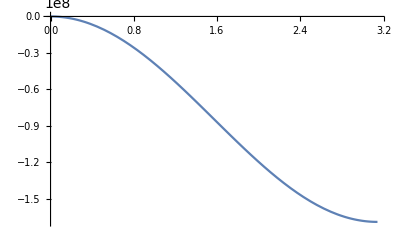

```mathematica
Plot[tmp1/.{MB->4.7,MH->125,e->(13000^2-4.7^2)/26000},{th,0,Pi}]
```

```mathematica
tmp1/.{MB->4.7,MH->125,e->(13000^2-4.7^2)/26000}
```

44.18-2 (4.22461×10^7-4.22461×10^7 cos(th))

```mathematica
Cases[amp,_LorentzIndex,Infinity]//DeleteDuplicates
```

{Lor1}

```mathematica
Clear[hf]
```

```mathematica
(*p[5] polvec, p[6] polvec Conjugate*)
ampSp=FV[p[5],Lor1] FV[p[6],Lor2] (spinsum[p[3],hf].(ComplexConjugate[amp]/.Lor1->Lor2).spinsum[p[1],hi].amp)//PropagatorDenominatorExplicit//ChangeDimension[#,4]&//Contract//TR//SUNSimplify;
ampSm=FV[p[7],Lor1] FV[p[8],Lor2] (spinsum[p[3],hf].(ComplexConjugate[amp]/.Lor1->Lor2).spinsum[p[1],hi].amp)//PropagatorDenominatorExplicit//ChangeDimension[#,4]&//Contract//TR//SUNSimplify;
```

```mathematica
eps[p[a_],p[b_],p[c_],p[d_]]:=Plus@@(q[a][[#[[1]]]] q[b][[#[[2]]]] q[c][[#[[3]]]] q[d][[#[[4]]]]&/@{{1,2,3,4},{1,3,4,2},{1,4,2,3},{2,1,4,3},{2,4,3,1},{2,3,1,4},{3,1,2,4},{3,2,4,1},{3,4,1,2},{4,1,3,2},{4,3,2,1},{4,2,1,3}})-Plus@@(q     [a][[#[[1]]]] q[b][[#[[2]]]] q[c][[#[[3]]]] q[d][[#[[4]]]]&/@{{1,3,2,4},{1,2,4,3},{1,4,3,2},{2,1,3,4},{2,3,4,1},{2,4,1,3},{3,1,4,2},{3,4,2,1},{3,2,1,4},{4,1,2,3},{4,2,3,1},{4,3,1,2}});
```

```mathematica
ampSp=ampSp//ReplaceAll[#,{Eps[Momentum[p[a_]],Momentum[p[b_]],Momentum[p[c_]],Momentum[p[d_]]]:>eps[p[a],p[b],p[c],p[d]]}]&;
ampSm=ampSm//ReplaceAll[#,{Eps[Momentum[p[a_]],Momentum[p[b_]],Momentum[p[c_]],Momentum[p[d_]]]:>eps[p[a],p[b],p[c],p[d]]}]&;
```

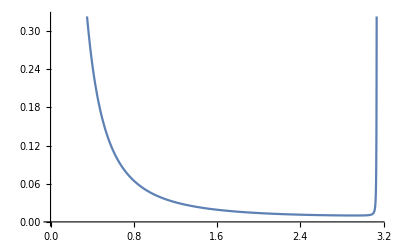

```mathematica
Plot[ampSp/.{MB->4.7,MH->125,e->(13000^2-4.7^2)/26000,hi->1,hf->1,ybcky->4.7/246,gs->1,ghcky->0.1/12/Pi/246,al->0,CA->1,CF->1},{th,0,Pi}]
```

```mathematica
ampSp/.{MB->4.7,MH->125,e->(13000^2-4.7^2)/26000,hi->1,hf->1,ybcky->4.7/246,gs->1,ghcky->0.1/12/Pi/246,al->0,CA->1,CF->1}//FullSimplify
```

(0.00491218 cos(th)-0.00982641 cos(2 th)-0.00491218 cos(3 th)-1.71152×10^-7 cos(4 th)-1.47561×10^-12 cos(5 th)+0.00982658)/((cos(th) (1. cos(th)+2.61461×10^-7)-1.)^2)

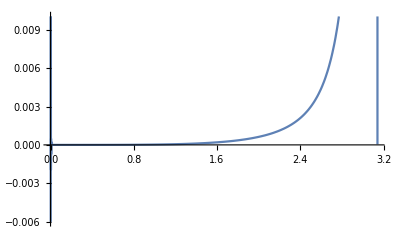

```mathematica
Plot[ampSp/.{MB->4.7,MH->125,e->(13000^2-4.7^2)/26000,hi->1,hf->-1,ybcky->4.7/246,gs->1,ghcky->0.1/12/Pi/246,al->0,CA->1,CF->1},{th,0.,Pi}]
```

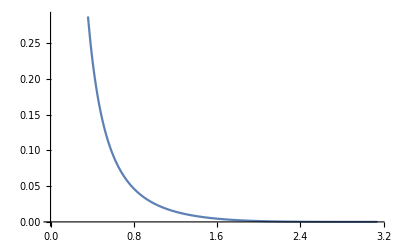

```mathematica
Plot[ampSp/.{MB->4.7,MH->125,e->(13000^2-4.7^2)/26000,hi->-1,hf->-1,ybcky->4.7/246,gs->1,ghcky->0.1/12/Pi/246,al->0,CA->1,CF->1},{th,0.,Pi}]
```

```mathematica
Plot[ampSm/.{MB->4.7,MH->125,e->(13000^2-4.7^2)/26000,hi->1,hf->1,ybcky->4.7/246,gs->1,ghcky->0.1/12/Pi/246,al->0,CA->1,CF->1},{th,0.,Pi}]
```

-Graphics-

```mathematica
Plot[ampSm/.{MB->4.7,MH->125,e->(13000^2-4.7^2)/26000,hi->-1,hf->-1,ybcky->4.7/246,gs->1,ghcky->0.1/12/Pi/246,al->0,CA->1,CF->1}//FullSimplify,{th,0,Pi}]
```

-Graphics-

```mathematica
ampSm/.{MB->4.7,MH->125,e->(13000^2-4.7^2)/26000,hi->-1,hf->-1,ybcky->4.7/246,gs->1,ghcky->0.1/12/Pi/246,al->0,CA->1,CF->1}//FullSimplify
```

(0.00491218 cos(th)-0.00982641 cos(2 th)-0.00491218 cos(3 th)-1.71152×10^-7 cos(4 th)-1.47561×10^-12 cos(5 th)+0.00982658)/((cos(th) (1. cos(th)+2.61461×10^-7)-1.)^2)

```mathematica
Plot[ampSm/.{MB->4.7,MH->125,e->(13000^2-4.7^2)/26000,hi->-1,hf->1,ybcky->4.7/246,gs->1,ghcky->0.1/12/Pi/246,al->0,CA->1,CF->1}//FullSimplify,{th,0,Pi}]
```

-Graphics-

```mathematica
ampSm/.{MB->4.7,MH->125,e->(13000^2-4.7^2)/26000,hi->-1,hf->1,ybcky->4.7/246,gs->1,ghcky->0.1/12/Pi/246,al->0,CA->1,CF->1,th->3.14}//FullSimplify
```

395.709+0. ⅈ